## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/primary-repos/github/experiment-mathematica/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="rcs/fourier/search/";  
Get["utility modules.m",Path->dirPack];
Get["rcs-tools-01.m",Path->dirnb<>"rcs/tools/"];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/primary-repos/github/experiment-mathematica/io/ already exists.

CreateDirectory::filex: /Users/dantopa/primary-repos/github/experiment-mathematica/io/rcs/ already exists.

CreateDirectory::filex: /Users/dantopa/primary-repos/github/experiment-mathematica/io/rcs/fourier/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.170457 GB

seed file: /Users/dantopa/primary-repos/github/experiment-mathematica/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: May 2, 2020, time: 14:38:49

nb: /Users/dantopa/primary-repos/github/experiment-mathematica/nb/rcs/fourier/search/nelson-writer-02.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.170457 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,5},{Automatic,5}};
```

```mathematica
isize=ImageSize->5 72;
```

```mathematica
ftickspi={{-π,-180°},{-π/2,-90°},{0,"0°"},{π/2,90°},{π,180°}};
```

```mathematica
optA={ipad,Frame->True,FrameLabel->{labelyaw,labelrcs},FrameTicks->{{Automatic,Automatic},{fticks180,Automatic}}};
```

#### functions

#### substitutions

#### modules

### tagger

```mathematica
Clear[tagSource];
tagSource[str_OutputStream]:=Module[{},
(* tag Mathematica file *)
Write[str,"% ",nb];
Write[str,"% ",dirHome];
mark;
Write[str,"% ","user: ",user,", CPU: ",CPU,", MM v. ",mmv];
Write[str,"% ",time," ",date];
Write[str,""];
]
```

## import

```mathematica
σ=Import[dirDataLocker<>sciaccarcs];
Dimensions[σ]
λ=Length[σ]
```

{28,361}

28

## te sweep

## data

```mathematica
te={{0,41432.59924004194},{1,41279.82709432303},{2,35341.93142483971},{3,35232.038183200304},{4,31509.980992337176},{5,31342.907372794467},{6,26239.450407402226},{7,26138.975841541727},{8,19754.09755880866},{9,19530.891172701442},{10,11780.167960269991},{11,11199.669693384361},{12,6020.0294180234405},{13,6019.674364161749},{14,3346.3240385026406},{15,3335.064500398022},{16,1757.150767103065},{17,1748.9899746103351},{18,1533.4665549024116},{19,1439.8366171055256},{20,1220.6879629391037},{21,1152.8055528746454},{22,929.2972733034002},{23,888.3979440993342},{24,609.079216152579},{25,578.1948813549193},{26,447.86958443521996},{27,434.36479575116823},{28,394.8450522248506},{29,389.88275401011526},{30,285.49377854446993},{31,277.363937993306},{32,173.86410036876316},{33,173.8271503576469},{34,99.24435543498277},{35,94.03121984630064},{36,79.28336249094991},{37,73.71323260976592},{38,70.89187037277374},{39,65.82341514389455},{40,65.24875811308513},{41,64.1676948436192},{42,55.322315479788514},{43,54.2339358742483},{44,39.19764067901612},{45,39.18242956496259},{46,33.06125765012641},{47,32.36517437252303},{48,30.99503486555957},{49,30.022778794778066},{50,29.570862415720416}};
```

### plot bar

```mathematica
d=45;
```

```mathematica
grect=Graphics[{Black,Thick,EdgeForm[Thick],White,Rectangle[{0,0},{10,1}]}]
max=Max[te[[All,2]]];
min=Min[te[[All,2]]];
x=Log[10,50000]/Log[10,50000]
x=Log[10,41000]/Log[10,50000]//N
```

-Graphics-

1

0.981659

```mathematica
Table[
y=Log[10,x]/Log[10,50000]
,{x,{1,10,100,1000,10000}}]//N
```

{0.,0.212813,0.425625,0.638438,0.85125}

```mathematica
Log[10,4.1]
```

0.612784

```mathematica
λ=(10-Log[10,4.143259924004194])/3
```

3.12755

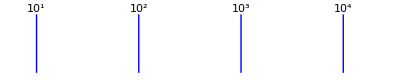

```mathematica
(* scale lines *)
glines=Table[
Line[{{k λ,0},{k λ,1.1}}]
,{k,0,3}];
scale=Graphics[{Blue,glines}];
(* label ticks *)
gl=Table[
Text[Superscript[10,k+1],{k λ,1.1},{0,-1}]
,{k,0,3}];
glabels=Graphics[{gl}];
(* assemble *)
gbar=Show[grect,scale,glabels]
```

```mathematica
tag=46;
te[[tag]]
val=te[[tag,2]]
```

{45,39.1824}

```mathematica
Log[10,val]
```

1.59309

0

1.59309

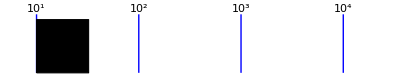

```mathematica
offset=IntegerPart[Log[10,val]]-1
z=λ offset+Log[10,val]
gerr=Graphics[{Thick,EdgeForm[Thick],Black,Rectangle[{0,0},{z,1}]}];
gmark=Graphics[Text["▲",{z,0},{0,1}]];Show[{gbar,gerr}]
```

### frequency bar

```mathematica
tbl=Table[
Rectangle[{k-1,0},{k,2}]
,{k,28}];
base=Graphics[{Black,Thick,EdgeForm[Thick],White,tbl}];
```

Rectangle[{21,0},{22,2}]

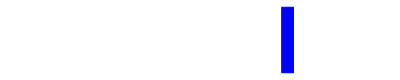

```mathematica
nu=22;
rect=Rectangle[{nu-1,0},{nu,2}]
slot=Graphics[{Black,Thick,EdgeForm[Thick],Blue,rect}];
Show[base,slot]
```

### plots

```mathematica
gte=ListLogPlot[te,
ipad,
(* PlotLabel->"Total Squared Error", *)
Frame->True,
FrameLabel->{"Degree of fit","‖r‖_2^2"},
PlotStyle->Black];
```

```mathematica
Clear[markPoint];
markPoint[δ_,g_Graphics]:=Module[{},
hi=Log[80000];
lo=Log[1];
ghor=Line[{{d,lo},{d,hi}}];
h=Log[te[[d+1,2]]];
gver=Line[{{-1,h},{51,h}}];
gmark=Graphics[{Gray,Opacity[0.5],ghor,gver}];
Return[Show[{g,gmark}]]
]
```

## ν, d

```mathematica
mesh=Range[-180,180];
```

```mathematica
$tick;
ψ=OpenWrite[dirData<>"sweep-A.dat",PageWidth->∞];
Do[
knu=nu-2;
b=σ[[knu]];
b2=b.b;
brange=Max[b]-Min[b];
resrange={nu};
resratio={nu};
$tick;
Clear[δ];
Do[
(* linear system *)
Clear[basis];
basis[θ_]:=Table[Cos[k θ],{k,0,δ}];
(* build linear system *)
A=BuildAFourierCos[mesh,δ];
(* least squares solution *)
x=LeastSquares[A,b];
(* error analysis *)
error[A//N,x,b];
var=Max[residual]-Min[residual];
resrange=AppendTo[resrange,Round[1000(1-var/brange)]/10//N];
,{δ,0,10}];
Write[ψ,resrange];
,{nu,3,30}]
tiempo["sweeps"];
Close[ψ];
```

sweeps
CPU time: 0.721734 sec
elapsed time: 0.121640 sec

## another sweep

```mathematica
rangeTable=Table[
knu=nu-2;
b=σ[[knu]];
{nu,Max[b]-Min[b]}
,{nu,3,30}]
```

{{3,17.4506},{4,27.7011},{5,40.8454},{6,39.2399},{7,28.7571},{8,32.7449},{9,36.0556},{10,35.1333},{11,39.1227},{12,43.9792},{13,46.9099},{14,49.9082},{15,54.2608},{16,55.8633},{17,56.1105},{18,52.2938},{19,45.4934},{20,45.156},{21,46.9024},{22,44.3495},{23,45.6654},{24,46.319},{25,47.5099},{26,49.3833},{27,51.5243},{28,51.3238},{29,52.3434},{30,54.5709}}

```mathematica
g=ListPlot[rangeTable,
PlotRange->{{2.5,30.5},{-1,65}};
FrameLabel->{"Frequency, MHz","RCS Variation, sq m"},
PlotStyle->Black,
Frame->True];
multiExport["agg-rcs-variation",g]
```

### loop

```mathematica
mesh=Range[-180,180];
```

```mathematica
ψ=OpenWrite[dirData<>"sweep-abs.dat",PageWidth->∞];
ϕ=OpenWrite[dirData<>"sweep-pcnt.dat",PageWidth->∞];
φ=OpenWrite[dirData<>"sweep-te.dat",PageWidth->∞];
threshold=0.9;
Do[
(* linear system *)
Clear[basis];
basis[θ_]:=Table[Cos[k θ],{k,0,δ}];
(* build linear system *)
A=BuildAFourierCos[mesh,δ];
te={};
list={δ};
listpcnt={δ};
listtf={δ};
Do[
knu=nu-2;
b=σ[[knu]];
var=Max[b]-Min[b];
(* least squares solution *)
x=LeastSquares[A,b];
(* error analysis *)
error[A//N,x,b];
(* variation *)
resrange=Max[residual]-Min[residual];
respcnt=Chop[1-resrange/var];
list=AppendTo[list,resrange];
listpcnt=AppendTo[listpcnt,Round[1000respcnt]/10//N];
good=If[respcnt≥threshold,"YES","NO","Null"];
te=AppendTo[te,totalError];
listtf=AppendTo[listtf,good];
,{nu,3,16}]
Write[ψ,list]
Write[ϕ,listpcnt]
Write[φ,te]
,{δ,0,25}];
Close[ψ];
Close[ϕ];Close[φ];
```

## mark locations

```mathematica
rangeTable=Table[
knu=nu-2;
b=σ[[knu]];
{nu,Max[b]-Min[b]}
,{nu,3,30}]
```

{{3,17.4506},{4,27.7011},{5,40.8454},{6,39.2399},{7,28.7571},{8,32.7449},{9,36.0556},{10,35.1333},{11,39.1227},{12,43.9792},{13,46.9099},{14,49.9082},{15,54.2608},{16,55.8633},{17,56.1105},{18,52.2938},{19,45.4934},{20,45.156},{21,46.9024},{22,44.3495},{23,45.6654},{24,46.319},{25,47.5099},{26,49.3833},{27,51.5243},{28,51.3238},{29,52.3434},{30,54.5709}}

```mathematica
g=ListPlot[rangeTable,
PlotRange->{{2.5,30.5},{-1,65}};
FrameLabel->{"Frequency, MHz","RCS Variation, sq m"},
PlotStyle->Black,
Frame->True];
multiExport["agg-rcs-variation",g]
```

### loop

```mathematica
mesh=Range[-180,180];
```

```mathematica
ψ=OpenWrite[dirData<>"sweep-abs.dat",PageWidth->∞];
ϕ=OpenWrite[dirData<>"sweep-pcnt.dat",PageWidth->∞];
φ=OpenWrite[dirData<>"sweep-te.dat",PageWidth->∞];
threshold=0.9;
Do[
(* linear system *)
Clear[basis];
basis[θ_]:=Table[Cos[k θ],{k,0,δ}];
(* build linear system *)
A=BuildAFourierCos[mesh,δ];
te={};
list={δ};
listpcnt={δ};
listtf={δ};
Do[
knu=nu-2;
b=σ[[knu]];
var=Max[b]-Min[b];
(* least squares solution *)
x=LeastSquares[A,b];
(* error analysis *)
error[A//N,x,b];
(* variation *)
resrange=Max[residual]-Min[residual];
respcnt=Chop[1-resrange/var];
list=AppendTo[list,resrange];
listpcnt=AppendTo[listpcnt,Round[1000respcnt]/10//N];
good=If[respcnt≥threshold,"YES","NO","Null"];
te=AppendTo[te,totalError];
listtf=AppendTo[listtf,good];
,{nu,3,16}]
Write[ψ,list]
Write[ϕ,listpcnt]
Write[φ,te]
,{δ,0,25}];
Close[ψ];
Close[ϕ];Close[φ];
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```